```mathematica
h0 =-m{{0,(px-I py)^2},{(px+I py)^2,0}}; (*m depends only on gamma0, gamma3*)
hw =v3{{0,(px + I py)},{(px - I py), 0}} ; (* v3 depends only on gamma3*)
H = Simplify[h0 + hw];
GIm = Inverse[I ω - H];
Simplify[GIm[[1,1]]]
```

-(ⅈ ω)/(m^2 (px^2+py^2)^2+v3 (px^2 v3+py^2 v3-2 ⅈ px ω)+m (-2 px^3 v3+6 px py^2 v3+2 ⅈ px^2 ω-2 ⅈ py^2 ω))

```mathematica
Integrate[-ω/(m^2 (px^2+py^2)^2+v3 (px^2 v3+py^2 v3-2px(ω + I η) )+m (-2 px^3 v3+6 px py^2 v3+2 (px^2-py^2)(ω+I η) )),{py,-Infinity,Infinity},GenerateConditions->False]
```

-((m π ω (-((-1)^Floor[(π-2 Arg[m]+Arg[2 m^2 px^2+6 m px v3+v3^2-2 ⅈ m η+√(v3^4+4 m^2 (9 px^2 v3^2+px v3 (-4 ⅈ η-4 ω)-(η-ⅈ ω)^2)+16 m^3 px^2 (2 px v3-ⅈ η-ω)+4 m v3^2 (3 px v3-ⅈ η-ω))-2 m ω])/(2 π)])/(√(2 m^2 px^2+v3^2+√(v3^4+4 m^2 (9 px^2 v3^2+px v3 (-4 ⅈ η-4 ω)-(η-ⅈ ω)^2)+16 m^3 px^2 (2 px v3-ⅈ η-ω)+4 m v3^2 (3 px v3-ⅈ η-ω))+m (6 px v3-2 ⅈ η-2 ω)))+(ⅈ (-1)^Floor[(-2 Arg[m]+Arg[-2 m^2 px^2-6 m px v3-v3^2+2 ⅈ m η+√(v3^4+4 m^2 (9 px^2 v3^2+px v3 (-4 ⅈ η-4 ω)-(η-ⅈ ω)^2)+16 m^3 px^2 (2 px v3-ⅈ η-ω)+4 m v3^2 (3 px v3-ⅈ η-ω))+2 m ω])/(2 π)])/(√(-2 m^2 px^2-v3^2+√(v3^4+4 m^2 (9 px^2 v3^2+px v3 (-4 ⅈ η-4 ω)-(η-ⅈ ω)^2)+16 m^3 px^2 (2 px v3-ⅈ η-ω)+4 m v3^2 (3 px v3-ⅈ η-ω))+m (-6 px v3+2 ⅈ η+2 ω)))))/(√(v3^4/2+2 m^2 (9 px^2 v3^2+px v3 (-4 ⅈ η-4 ω)-(η-ⅈ ω)^2)+8 m^3 px^2 (2 px v3-ⅈ η-ω)+2 m v3^2 (3 px v3-ⅈ η-ω))))

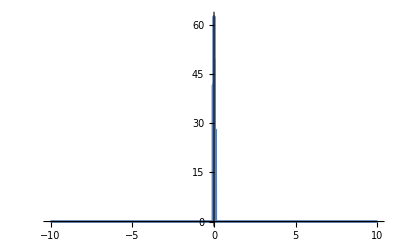

```mathematica
Plot[-Im[-((m π ω (-((-1)^Floor[(π-2 Arg[m]+Arg[2 m^2 px^2+6 m px v3+v3^2-2 ⅈ m η+√(v3^4+4 m^2 (9 px^2 v3^2+px v3 (-4 ⅈ η-4 ω)-(η-ⅈ ω)^2)+16 m^3 px^2 (2 px v3-ⅈ η-ω)+4 m v3^2 (3 px v3-ⅈ η-ω))-2 m ω])/(2 π)])/(√(2 m^2 px^2+v3^2+√(v3^4+4 m^2 (9 px^2 v3^2+px v3 (-4 ⅈ η-4 ω)-(η-ⅈ ω)^2)+16 m^3 px^2 (2 px v3-ⅈ η-ω)+4 m v3^2 (3 px v3-ⅈ η-ω))+m (6 px v3-2 ⅈ η-2 ω)))+(ⅈ (-1)^Floor[(-2 Arg[m]+Arg[-2 m^2 px^2-6 m px v3-v3^2+2 ⅈ m η+√(v3^4+4 m^2 (9 px^2 v3^2+px v3 (-4 ⅈ η-4 ω)-(η-ⅈ ω)^2)+16 m^3 px^2 (2 px v3-ⅈ η-ω)+4 m v3^2 (3 px v3-ⅈ η-ω))+2 m ω])/(2 π)])/(√(-2 m^2 px^2-v3^2+√(v3^4+4 m^2 (9 px^2 v3^2+px v3 (-4 ⅈ η-4 ω)-(η-ⅈ ω)^2)+16 m^3 px^2 (2 px v3-ⅈ η-ω)+4 m v3^2 (3 px v3-ⅈ η-ω))+m (-6 px v3+2 ⅈ η+2 ω)))))/(√(v3^4/2+2 m^2 (9 px^2 v3^2+px v3 (-4 ⅈ η-4 ω)-(η-ⅈ ω)^2)+8 m^3 px^2 (2 px v3-ⅈ η-ω)+2 m v3^2 (3 px v3-ⅈ η-ω))))/.{m->1, v3->0.1, η-> 0.00001,ω->0.001}], {px,-10,10},PlotRange->Full]
```

```mathematica
NIntegrate[-Im[-((m π ω (-((-1)^Floor[(π-2 Arg[m]+Arg[2 m^2 px^2+6 m px v3+v3^2-2 ⅈ m η+√(v3^4+4 m^2 (9 px^2 v3^2+px v3 (-4 ⅈ η-4 ω)-(η-ⅈ ω)^2)+16 m^3 px^2 (2 px v3-ⅈ η-ω)+4 m v3^2 (3 px v3-ⅈ η-ω))-2 m ω])/(2 π)])/(√(2 m^2 px^2+v3^2+√(v3^4+4 m^2 (9 px^2 v3^2+px v3 (-4 ⅈ η-4 ω)-(η-ⅈ ω)^2)+16 m^3 px^2 (2 px v3-ⅈ η-ω)+4 m v3^2 (3 px v3-ⅈ η-ω))+m (6 px v3-2 ⅈ η-2 ω)))+(ⅈ (-1)^Floor[(-2 Arg[m]+Arg[-2 m^2 px^2-6 m px v3-v3^2+2 ⅈ m η+√(v3^4+4 m^2 (9 px^2 v3^2+px v3 (-4 ⅈ η-4 ω)-(η-ⅈ ω)^2)+16 m^3 px^2 (2 px v3-ⅈ η-ω)+4 m v3^2 (3 px v3-ⅈ η-ω))+2 m ω])/(2 π)])/(√(-2 m^2 px^2-v3^2+√(v3^4+4 m^2 (9 px^2 v3^2+px v3 (-4 ⅈ η-4 ω)-(η-ⅈ ω)^2)+16 m^3 px^2 (2 px v3-ⅈ η-ω)+4 m v3^2 (3 px v3-ⅈ η-ω))+m (-6 px v3+2 ⅈ η+2 ω)))))/(√(v3^4/2+2 m^2 (9 px^2 v3^2+px v3 (-4 ⅈ η-4 ω)-(η-ⅈ ω)^2)+8 m^3 px^2 (2 px v3-ⅈ η-ω)+2 m v3^2 (3 px v3-ⅈ η-ω))))/.{m->1, v3->0.1, η-> 0.00001,ω->0.001}], {px,-Pi,Pi},Method->"GlobalAdaptive",MinRecursion->200,MaxRecursion->1000,AccuracyGoal->10, IntegrationMonitor :>((errors=Through[#1@"Error"])&)]
Length@errors
Total@errors
```

$Aborted

1039

0.0174189

```mathematica
strreprule = {"Pi"-> "np.pi", "Sqrt"->"np.sqrt", "η"->"eta", "Arg"->"np.angle", "Floor"->"np.floor", "ω"->"omega","Im"->"np.imag" };
```

```mathematica
StringReplace[(m π ω Im[(-((-1)^Floor[(π+Arg[2 m^2 px^2+6 m px v3+v3^2-2 ⅈ m η+√(v3^4+4 m^2 (9 px^2 v3^2+px v3 (-4 ⅈ η-4 ω)-(η-ⅈ ω)^2)+16 m^3 px^2 (2 px v3-ⅈ η-ω)+4 m v3^2 (3 px v3-ⅈ η-ω))-2 m ω])/(2 π)])/(√(2 m^2 px^2+v3^2+√(v3^4+4 m^2 (9 px^2 v3^2+px v3 (-4 ⅈ η-4 ω)-(η-ⅈ ω)^2)+16 m^3 px^2 (2 px v3-ⅈ η-ω)+4 m v3^2 (3 px v3-ⅈ η-ω))+m (6 px v3-2 ⅈ η-2 ω)))+(ⅈ (-1)^Floor[Arg[-2 m^2 px^2-v3^2+√(v3^4+4 m^2 (9 px^2 v3^2+px v3 (-4 ⅈ η-4 ω)-(η-ⅈ ω)^2)+16 m^3 px^2 (2 px v3-ⅈ η-ω)+4 m v3^2 (3 px v3-ⅈ η-ω))+2 m (-3 px v3+ⅈ η+ω)]/(2 π)])/(√(-2 m^2 px^2-v3^2+√(v3^4+4 m^2 (9 px^2 v3^2+px v3 (-4 ⅈ η-4 ω)-(η-ⅈ ω)^2)+16 m^3 px^2 (2 px v3-ⅈ η-ω)+4 m v3^2 (3 px v3-ⅈ η-ω))+2 m (-3 px v3+ⅈ η+ω))))/(√(v3^4/2+2 m^2 (9 px^2 v3^2+px v3 (-4 ⅈ η-4 ω)-(η-ⅈ ω)^2)+8 m^3 px^2 (2 px v3-ⅈ η-ω)+2 m v3^2 (3 px v3-ⅈ η-ω)))]//FortranForm //ToString //StringReplace[strreprule]), RegularExpression["\\(0,([^()]+)\\)"] :> "$1j"]
```

m*np.pi*omega*np.imag((-((-1)**np.floor((np.pi + np.angle(2*m**2*px**2 + 6*m*px*v3 + v3**2 - 2j*m*eta + np.sqrt(v3**4 + 4*m**2*(9*px**2*v3**2 + px*v3*(-4j*eta - 4*omega) - (eta - 1j*omega)**2) + 16*m**3*px**2*(2*px*v3 - 1j*eta - omega) + 4*m*v3**2*(3*px*v3 - 1j*eta - omega)) - 2*m*omega))/(2.*np.pi))/np.sqrt(2*m**2*px**2 + v3**2 + np.sqrt(v3**4 + 4*m**2*(9*px**2*v3**2 + px*v3*(-4j*eta - 4*omega) - (eta - 1j*omega)**2) + 16*m**3*px**2*(2*px*v3 - 1j*eta - omega) + 4*m*v3**2*(3*px*v3 - 1j*eta - omega)) + m*(6*px*v3 - 2j*eta - 2*omega))) + (1j*(-1)**np.floor(np.angle(-2*m**2*px**2 - v3**2 + np.sqrt(v3**4 + 4*m**2*(9*px**2*v3**2 + px*v3*(-4j*eta - 4*omega) - (eta - 1j*omega)**2) + 16*m**3*px**2*(2*px*v3 - 1j*eta - omega) + 4*m*v3**2*(3*px*v3 - 1j*eta - omega)) + 2*m*(-3*px*v3 + 1j*eta + omega))/(2.*np.pi)))/np.sqrt(-2*m**2*px**2 - v3**2 + np.sqrt(v3**4 + 4*m**2*(9*px**2*v3**2 + px*v3*(-4j*eta - 4*omega) - (eta - 1j*omega)**2) + 16*m**3*px**2*(2*px*v3 - 1j*eta - omega) + 4*m*v3**2*(3*px*v3 - 1j*eta - omega)) + 2*m*(-3*px*v3 + 1j*eta + omega)))/np.sqrt(v3**4/2. + 2*m**2*(9*px**2*v3**2 + px*v3*(-4j*eta - 4*omega) - (eta - 1j*omega)**2) + 8*m**3*px**2*(2*px*v3 - 1j*eta - omega) + 2*m*v3**2*(3*px*v3 - 1j*eta - omega)))

```mathematica
FullSimplify[-Im[-((m π ω (-((-1)^Floor[(π-2 Arg[m]+Arg[2 m^2 px^2+6 m px v3+v3^2-2 ⅈ m η+√(v3^4+4 m^2 (9 px^2 v3^2+px v3 (-4 ⅈ η-4 ω)-(η-ⅈ ω)^2)+16 m^3 px^2 (2 px v3-ⅈ η-ω)+4 m v3^2 (3 px v3-ⅈ η-ω))-2 m ω])/(2 π)]/(√(2 m^2 px^2+v3^2+√(v3^4+4 m^2 (9 px^2 v3^2+px v3 (-4 ⅈ η-4 ω)-(η-ⅈ ω)^2)+16 m^3 px^2 (2 px v3-ⅈ η-ω)+4 m v3^2 (3 px v3-ⅈ η-ω))+m (6 px v3-2 ⅈ η-2 ω))))+(ⅈ (-1)^Floor[(-2 Arg[m]+Arg[-2 m^2 px^2-6 m px v3-v3^2+2 ⅈ m η+√(v3^4+4 m^2 (9 px^2 v3^2+px v3 (-4 ⅈ η-4 ω)-(η-ⅈ ω)^2)+16 m^3 px^2 (2 px v3-ⅈ η-ω)+4 m v3^2 (3 px v3-ⅈ η-ω))+2 m ω])/(2 π)])/(√(-2 m^2 px^2-v3^2+√(v3^4+4 m^2 (9 px^2 v3^2+px v3 (-4 ⅈ η-4 ω)-(η-ⅈ ω)^2)+16 m^3 px^2 (2 px v3-ⅈ η-ω)+4 m v3^2 (3 px v3-ⅈ η-ω))+m (-6 px v3+2 ⅈ η+2 ω)))))/(√(v3^4/2+2 m^2 (9 px^2 v3^2+px v3 (-4 ⅈ η-4 ω)-(η-ⅈ ω)^2)+8 m^3 px^2 (2 px v3-ⅈ η-ω)+2 m v3^2 (3 px v3-ⅈ η-ω))))],{ω>0, m>0, v3>0, η>0}]
```

m π ω Im[(-((-1)^Floor[(π+Arg[2 m^2 px^2+6 m px v3+v3^2-2 ⅈ m η+√(v3^4+4 m^2 (9 px^2 v3^2+px v3 (-4 ⅈ η-4 ω)-(η-ⅈ ω)^2)+16 m^3 px^2 (2 px v3-ⅈ η-ω)+4 m v3^2 (3 px v3-ⅈ η-ω))-2 m ω])/(2 π)])/(√(2 m^2 px^2+v3^2+√(v3^4+4 m^2 (9 px^2 v3^2+px v3 (-4 ⅈ η-4 ω)-(η-ⅈ ω)^2)+16 m^3 px^2 (2 px v3-ⅈ η-ω)+4 m v3^2 (3 px v3-ⅈ η-ω))+m (6 px v3-2 ⅈ η-2 ω)))+(ⅈ (-1)^Floor[Arg[-2 m^2 px^2-v3^2+√(v3^4+4 m^2 (9 px^2 v3^2+px v3 (-4 ⅈ η-4 ω)-(η-ⅈ ω)^2)+16 m^3 px^2 (2 px v3-ⅈ η-ω)+4 m v3^2 (3 px v3-ⅈ η-ω))+2 m (-3 px v3+ⅈ η+ω)]/(2 π)])/(√(-2 m^2 px^2-v3^2+√(v3^4+4 m^2 (9 px^2 v3^2+px v3 (-4 ⅈ η-4 ω)-(η-ⅈ ω)^2)+16 m^3 px^2 (2 px v3-ⅈ η-ω)+4 m v3^2 (3 px v3-ⅈ η-ω))+2 m (-3 px v3+ⅈ η+ω))))/(√(v3^4/2+2 m^2 (9 px^2 v3^2+px v3 (-4 ⅈ η-4 ω)-(η-ⅈ ω)^2)+8 m^3 px^2 (2 px v3-ⅈ η-ω)+2 m v3^2 (3 px v3-ⅈ η-ω)))]